```mathematica
Integrate[x*BesselJ[1,x]^2,x]
```

1/2 x^2 (BesselJ[1,x]^2-BesselJ[0,x] BesselJ[2,x])

```mathematica
Clear[x];
Integrate[x*BesselJ[1,x],x]
```

1/6 x^3 HypergeometricPFQ[{3/2},{2,5/2},-x^2/4]

```mathematica
BesselJ[1,0]
```

0

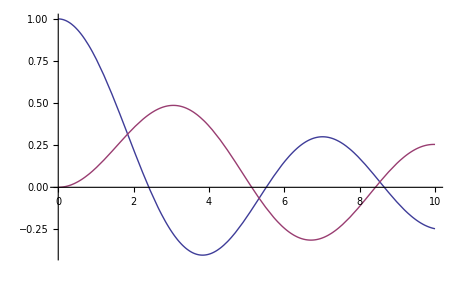

```mathematica
Plot[{BesselJ[0,x],BesselJ[2,x]},{x,0,10}]
```

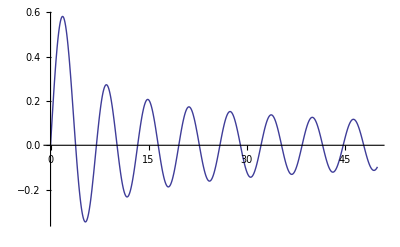

```mathematica
Plot[BesselJ[1,x],{x,0,50}]
```